### Bivariate Gaussian prior P_H

`R` : signal redundancy [in bits]

```mathematica
Clear[pH]
pH[x_,y_,R_]=2^R/(2π)Exp[-2^(2R)/2(x^2+y^2-2 √(1-2^(-2R))x*y)];
```

### Conditional & joint distribution P_(S|H) & P_(S,H)

See Eqs. (4,7,8) in the main text

`b` : sensor reliability
`J` : sensor coupling
`t` : nonequilibrium drive

```mathematica
Clear[pSconH,pSH,aSconH]
(*define unnormalised conditional distribution for convenience*)
aSconH[s1_,s2_,h1_,h2_,β_,J_,t_]:=ⅇ^(β(h1*s1+h2*s2+J*s1*s2))(ⅇ^(β(h1-s2 t+s1 s2 t/2))+ⅇ^(β(-h1+s2 t+s1 s2 t/2))+ⅇ^(β(-h2-s1 t- s1 s2 t/2))+ⅇ^(β(h2+s1 t-s1 s2 t/2)))
Do[
pSconH[s1,s2][x_,y_][b_,J_,t_]=aSconH[s1,s2,x,y,b,J,t]/Sum[aSconH[s1,s2,x,y,b,J,t],{s1,{-1,1}},{s2,{-1,1}}];

pSH[s1,s2][x_,y_][R_,b_,J_,t_]=(aSconH[s1,s2,x,y,b,J,t]pH[x,y,R])/Sum[aSconH[s1,s2,x,y,b,J,t],{s1,{-1,1}},{s2,{-1,1}}];

(*for special case t=0*)
pSconH[s1,s2][x_,y_][b_,J_,0]=ⅇ^(b(x*s1+y*s2+J*s1*s2))/Sum[ⅇ^(b(x*s1+y*s2+J*s1*s2)),{s1,{-1,1}},{s2,{-1,1}}];
pSH[s1,s2][x_,y_][R_,b_,J_,0]=(ⅇ^(b(x*s1+y*s2+J*s1*s2))pH[x,y,R])/Sum[ⅇ^(b(x*s1+y*s2+J*s1*s2)),{s1,{-1,1}},{s2,{-1,1}}];
,{s1,{-1,1}},{s2,{-1,1}}]

Clear[aSconH]
```

### Mutual information I(S;H)

`R` : signal redundancy [in bits]
`β` : sensor reliability
`J` : sensor coupling
`t` : nonequilibrium drive

```mathematica
Clear[infoSH]
infoSH[R_?NumericQ,β_?NumericQ,J_?NumericQ,t_?NumericQ]:=Block[
{qSconH,qSH,pS,kern,Sout,Sintegrand,Snoise,m={"LocalAdaptive","SymbolicProcessing"->0}},
Do[
qSconH[s1,s2]=pSconH[s1,s2][#1,#2][β,J,t]&;
qSH[s1,s2]=pSH[s1,s2][#1,#2][R,β,J,t]&;

pS[s1,s2]=NIntegrate[qSH[s1,s2][h1,h2],{h1,-∞,∞},{h2,-∞,∞},Method->m];

,{s1,{-1,1}},{s2,{-1,1}}];

(*Output entropy*)
Sout=Sum[pS[s1,s2]Log2[1/pS[s1,s2]],{s1,{-1,1}},{s2,{-1,1}}];

(*Noise entropy*)
Sintegrand[x_,y_]=Sum[-qSH[s1,s2][x,y]Log2[qSconH[s1,s2][x,y]],{s1,{-1,1}},{s2,{-1,1}}];

Snoise=NIntegrate[Sintegrand[h1,h2],{h1,-∞,∞},{h2,-∞,∞},Method->m];

(*Mutual information = Output entropy - Noise entropy*)
Sout-Snoise
]
```

### Equilibrium case

```mathematica
equilPlot[β_(*sensor reliability*),R_(*signal redundancy [bits]*)]:=With[{t=0},
optim=FindMaximum[infoSH[R,β,J,t],{J,-.1}];
Print["β = "<>ToString[β]<>";  I(h_1;h_2) = "<>ToString[R]<>" bits\n","Optimal equilibrium sensing : {I_eq^*(S;H), J_eq^*} = ",optim];
Print@ListPlot[#,AxesLabel->{"J","I(S;H) [bits]"},Epilog->{Red,PointSize[Large],Point[{J/.optim[[2]],optim[[1]]}]}]&@Table[{J,infoSH[R,β,J,t]},{J,-2.,2.,0.1}]
]
```

β = 2.;  I(h_1;h_2) = 2.5 bits
Optimal equilibrium sensing : {I_eq^*(S;H), J_eq^*} = {0.896935,{J→-0.319148}}

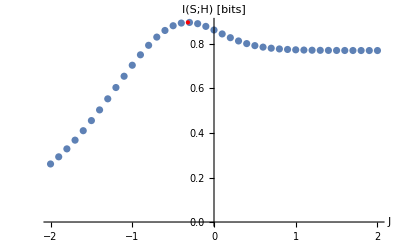

```mathematica
equilPlot[2.,2.5]
```

β = 3.;  I(h_1;h_2) = 2.5 bits
Optimal equilibrium sensing : {I_eq^*(S;H), J_eq^*} = {1.11701,{J→-0.420289}}

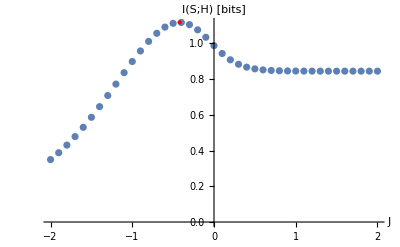

```mathematica
equilPlot[3.,2.5]
```

### Nonequilibrium case

```mathematica
optimNonequil[β_(*sensor reliability*),R_(*signal redundancy [bits]*)]:=(optim=FindMaximum[infoSH[R,β,J,t],{J,-.1},{t,0.01},PrecisionGoal->5];
Print["β = "<>ToString[β]<>";  I(h_1;h_2) = "<>ToString[R]<>" bits\n","Optimal equilibrium sensing : {I^*(S;H), {J^*,t^*}} = ",optim];)
```

```mathematica
optimNonequil[1.5,2.5]
```

β = 1.5;  I(h_1;h_2) = 2.5 bits
Optimal equilibrium sensing : {I^*(S;H), {J^*,t^*}} = {0.749178,{J→-0.116428,t→-4.16143×10^-8}}

```mathematica
optimNonequil[2.,2.5]
```

β = 2.;  I(h_1;h_2) = 2.5 bits
Optimal equilibrium sensing : {I^*(S;H), {J^*,t^*}} = {0.914511,{J→-0.489054,t→0.690847}}

```mathematica
optimNonequil[3.,2.5]
```

β = 3.;  I(h_1;h_2) = 2.5 bits
Optimal equilibrium sensing : {I^*(S;H), {J^*,t^*}} = {1.19892,{J→-0.557549,t→0.708406}}